# Automatically Deduce the Zoom for a Satellite Photo

## William Goodall

## Mentor: Zhamilya Bilyalova

## Abstract

We create an algorithm which, given a satellite image, can deduce the scale the image was taken at: which distance in the image corresponds with which distance over the pictured terrain. There are several approaches which can work to solve this problem. Using traditional image processing techniques, we can separate the image into high- and low-frequency information, and determine whether that correlates with zoom level. We can also take the machine learning approach, training a model on satellite images generated at different scales.

Initialize the environment

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Gathering Data

To get a training dataset, we can use the mapping and cartography features of the Wolfram Language. In particular, the GeoGraphics[] function lets us get satellite images of a given region. This lets us create a function to download high-resolution map images of a location and physical size we specify.

Define a function which retrieves satellite images of a given location and of a given diameter:

```mathematica
ClearAll[mapImage];
mapImage[location_, size_?NumericQ]:=
GeoImage[
GeoDisk[location, Quantity[size/2, "km"]],
GeoServer->"DigitalGlobe",
RasterSize->300
]
```

Retrieve a satellite image of the 100km region centered on Manhattan:

```mathematica
mapImage[Entity["AdministrativeDivision",{"NewYorkCounty","NewYork","UnitedStates"}], 100]
```

-Graphics-

This function also allows to get sets of images of the same location, all at different zoom levels:

Get 5 satellite images of Manhattan, at zoom levels ranging from 1 to 50 km across:

```mathematica
mapImage[Entity["AdministrativeDivision",{"NewYorkCounty","NewYork","UnitedStates"}], #]&/@{1, 5, 10, 20, 40}//Column
```

GeoServer::mlim: You have reached your monthly limit for high-resolution geo imagery. To request information on extending it, contact us at https://wolfr.am/mNYboAZD.

GeoImage::data: Unable to download data for ranges {{-73.9748,-73.9618},{44.7238,44.7369}} and zoom level 15 from geo server {DigitalGlobe,Layer→Satellite}.

GeoServer::mlim: You have reached your monthly limit for high-resolution geo imagery. To request information on extending it, contact us at https://wolfr.am/mNYboAZD.

GeoImage::data: Unable to download data for ranges {{-74.001,-73.9356},{44.6975,44.7631}} and zoom level 13 from geo server {DigitalGlobe,Layer→Satellite}.

GeoServer::mlim: You have reached your monthly limit for high-resolution geo imagery. To request information on extending it, contact us at https://wolfr.am/mNYboAZD.

General::stop: Further output of GeoServer::mlim will be suppressed during this calculation.

GeoImage::data: Unable to download data for ranges {{-74.0338,-73.903},{44.6649,44.7961}} and zoom level 12 from geo server {DigitalGlobe,Layer→Satellite}.

General::stop: Further output of GeoImage::data will be suppressed during this calculation.

GeoImage[GeoDisk[New York County (Manhattan), New York, United States,1/2 km],GeoServer→DigitalGlobe,RasterSize→300]
GeoImage[GeoDisk[New York County (Manhattan), New York, United States,5/2 km],GeoServer→DigitalGlobe,RasterSize→300]
GeoImage[GeoDisk[New York County (Manhattan), New York, United States,5 km],GeoServer→DigitalGlobe,RasterSize→300]
GeoImage[GeoDisk[New York County (Manhattan), New York, United States,10 km],GeoServer→DigitalGlobe,RasterSize→300]
GeoImage[GeoDisk[New York County (Manhattan), New York, United States,20 km],GeoServer→DigitalGlobe,RasterSize→300]

To gather a complete dataset, we also need a list of locations to test out. We can retrieve a random set of locations within the continental United States by calling RandomGeoPosition[]:

Retrieve a list of 100 random locations in the continental United States:

```mathematica
randomSample=RandomGeoPosition[Entity["Country","UnitedStates"],100]/.GeoPosition[locs_List]:> GeoPosition/@locs;
```

Store the locations in the notebook, so this analysis can be reproduced:

```mathematica
randomSample=;
```

Plot the locations on a map:

```mathematica
GeoGraphics[Point@randomSample]
```

-Graphics-

Using this dataset and the mapImage[] function we defined earlier, we can download a dataset of images, at varying zoom levels, of all these locations. We’ll store this in a Dataset[] for easy querying and retrieval. This will take a really long time, because it’s downloading a lot of images.

```mathematica
ClearAll[downloadImageBatch]
downloadImageBatch[locations_List, sizes_List]:=Module[
(* Show a progress indicator—this can take a REALLY long time *)
{total=Length[locations]*Length[sizes],current=0},
SetSharedVariable[current];
PrintTemporary[ProgressIndicator[Dynamic[current/total]]];

ParallelTable[
current =current+1;(* update progress indicator *)
<|"Location"->location, "Zoom"->zoom, "Image"->mapImage[location, zoom]|>,
{location, locations},
{zoom, sizes}
]//Flatten//Dataset
]
```

Download 4 zoom levels at each location in randomSample. This will take an incredibly long time if you don’t have the map tiles cached on your computer.

```mathematica
imageSet=downloadImageBatch[
(* use the randomized location dataset from earlier *)
randomSample,

(* use images at roughly-exponentially-decreasing zoom levels *)
{0.5,2, 10,20}
];

(* Save the dataset to disk *)
SetDirectory[NotebookDirectory[]];
DumpSave["dataset.mx", imageSet];
```

Load the dataset from disk, if you’ve downloaded it already:

```mathematica
Get["dataset.mx"]
```

Show the first few images in the dataset:

```mathematica
imageSet
```

Dataset[<>]

## trying Predict[]

The first option to predict the zoom level of each image is, well, to throw it into Predict[] and see what happens. To do this, we need to split each (image→ zoom level) pair into a test and training dataset, and train a model to predict the zoom level given the image.

Get (image → zoom level) pairs from the dataset, and split into training/test sets:

```mathematica
predictPairs=(#Image->#Zoom)&/@imageSet//Normal//RandomSample;
{predictTrain, predictTest} = TakeDrop[predictPairs, Length[predictPairs]*0.9];
Length/@{predictTrain, predictTest}
```

{360,40}

```mathematica
predictTest⟦;;3⟧
```

{-Graphics-→20,-Graphics-→2,-Graphics-→2}

Train the predictor

```mathematica
predictor=Predict[predictTrain, TargetDevice->"GPU", PerformanceGoal->"Quality"]
```

PredictorFunction[…]

This method sort of works, but doesn’t produce an accurate estimation. It works reasonably well for very small-scale images, and can fairly reliably tell the difference between very small- vs. very large-scale images. However, this model can’t reliably differentiate between the 20km and 10km zoom levels at all.

Plot expected predictions vs. actual map scales:

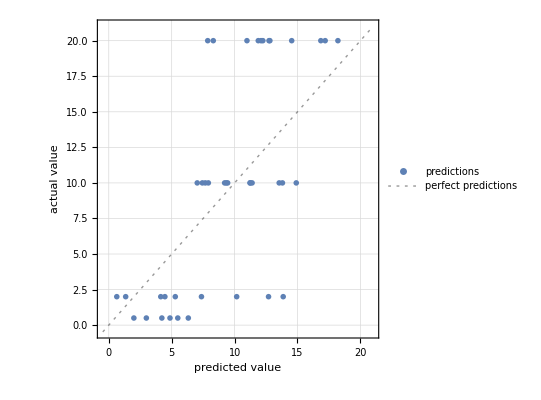

```mathematica
PredictorMeasurements[predictor, predictTest, "ComparisonPlot", TargetDevice->"GPU"]
```

## Extracting signals

Find an interesting Image → Number function, apply it to a scaled set of images, and plot the (hopefully interesting) result.

Histograms don’t really tell us anything: the total distribution of colors is roughly the same.

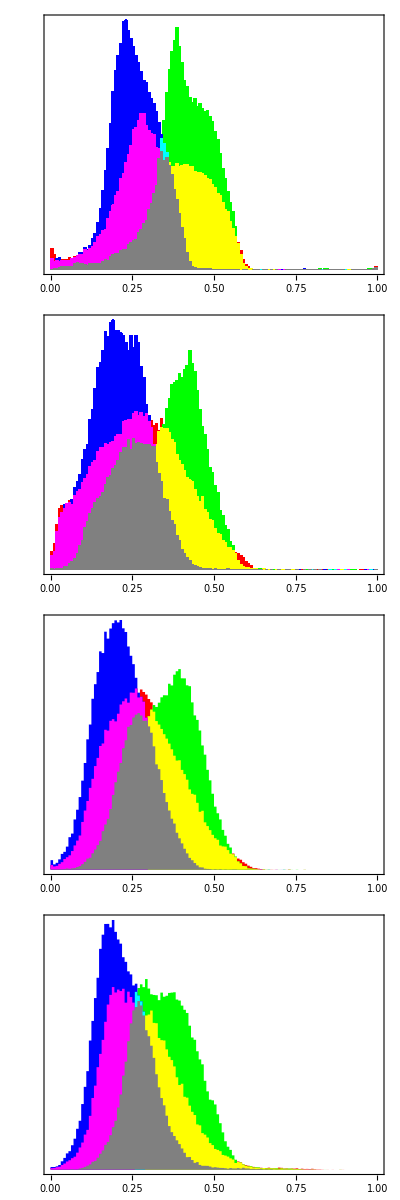

```mathematica
Column[ImageHistogram/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```